# Computer-Physik 1 Projekt

## 2022 Leon Oleschko

```mathematica
SetDirectory@NotebookDirectory[];
```

from https://www.cosmos.esa.int/web/ulysses/mission-trajectory :

```mathematica
d=Import["data/ulysses_daily_heliocentric_data_1990-2009.txt","Table"];
{Range@Length@d[[1]],d[[1]],Join[{"","","","","","","",""},d[[2]] ]}//TableForm
d=d[[4;;-1]];
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20
YYYY | MM | DD | YYYY | DOY | JD | HH | MM | SS | ESP | SPE | SEP | R | R | dR | V | lat | RA | DEC | long
 |  |  |  |  |  |  |  | [UTC] | [deg] | [deg] | [deg] | [AU] | [km] | [km/s] | [km/s] | [deg] | [deg] | [deg] | [deg]

```mathematica
selection = Range[10,529];
```

```mathematica
selection = Range[432,529];
```

```mathematica
selection = Range[10,3515];
```

## Historic Trajectory

```mathematica
hist =#[[1]] {
Cos[#[[2]] Degree]Cos[#[[3]] Degree],
Sin[#[[2]] Degree]Cos[#[[3]] Degree],
Sin[#[[3]] Degree]
}&/@d[[All,{13,18 ,19 }]];
```

```mathematica
plt=Graphics3D[{
(*Planet Orbits*)
Black,
AstronomicalData["Jupiter","OrbitPath"],
Text["Jupiter",{-4,-3,.5},Background->White],
AstronomicalData["Earth","OrbitPath"],
Text["Earth",{0,-1,.5},Background->White],
Point[{0,0,0}],

(*historic Trajectory*)
RGBColor[0.880722, 0.611041, 0.142051],
Line[hist[[1;;-1]]],
Text["Historic Trajectory",{Mean@hist[[All,1]],Mean@hist[[All,2]],Max@hist[[All,3]]}+{0,0,.7},Background->White],
(*selection*)
RGBColor[0., 0.6627450980392157, 0.8784313725490196],
Line[hist[[selection]]],
AbsolutePointSize[5],
Point[{hist[[Min@selection]],hist[[Max@selection]]}],
Text["Selection",hist[[500]]+{0,0,.7},Background->White]

},
Boxed->False,
Axes->True,
AxesLabel->{"x in AU","y in AU","z in AU"},
AxesStyle->Directive[10,FontColor->Black,FontFamily->"Times"],

FaceGrids->{{1,0,0},{0,0,-1},{0,-1,0}},
ViewPoint->100*{-4,6,2},ViewCenter->hist[[500]],ViewVertical->{0,0,1},

PlotRange->{{All,1.5},{-3,4},All},
ImageSize->Large
]
Export["img/trajectory.pdf",plt];
Export["img/trajectory.png",plt,ImageResolution->500];
```

-Graphics3D-

```mathematica
(*Export historic data*)
Export["data/spacecraft.csv",hist[[selection]],"Table"];
```

## Get Planet Positions

```mathematica
(*caching Planet Data*)
EntityPrefetch["Planet"];
cachedPlanetData[object_,dayoffset__]:=(
cachedPlanetData[object,dayoffset]=QuantityMagnitude@Entity["Planet",object][
"HelioCoordinates",{
"Date"->DatePlus[DateObject[d[[1,{1,2,3,7,8,9}]]+{0,0,0,0,0,1},TimeZone->"UTC"],
dayoffset]}
]
)
```

```mathematica
(*Takes approx. 30 min on the first time, dependig on Internet*)
jupiter=ResourceFunction["MonitorProgress"]@Map[cachedPlanetData["Jupiter",#]&,selection];//EchoTiming
earth=ResourceFunction["MonitorProgress"]@Map[cachedPlanetData["Earth",#]&,selection];//EchoTiming

sun=Table[{0,0,0},{i,selection}];

PrependTo[jupiter,{QuantityMagnitude@AstronomicalData["Jupiter","Mass"]}];
PrependTo[earth,{QuantityMagnitude@AstronomicalData["Earth","Mass"]}]; 
PrependTo[sun,{QuantityMagnitude@AstronomicalData["Sun","Mass"]}];

Export["data/planets/jupiter.csv",jupiter,"Table"];
Export["data/planets/earth.csv",earth, "Table"];
Export["data/planets/sun.csv",sun,"Table"];
```

```mathematica
(*import the data*)
jupiter=Import["data/planets/jupiter.csv","Table"];
earth=Import["data/planets/earth.csv","Table"];
sun=Import["data/planets/sun.csv","Table"];
```

## Starting Values

```mathematica
Max@selection-Min@selection
hist[[Min@selection]] (*AU*)
hist[[Min@selection+1]]-hist[[Min@selection]](*AU/day*)
```

519

{0.901865,0.424962,0.00748233}

{-0.00937424,0.0215741,0.000878397}

```mathematica
hist[[Max@selection]] (*AU*)
hist[[Max@selection+1]]-hist[[Max@selection]](*AU/day*)
```

```mathematica
{-4.99443408522095,2.0463303553843777,-0.08102002848437442}
```

```mathematica
{-0.00028974465364584034,-0.000899297755505124,-0.004710081570797581}
```

```mathematica
UnitConvert[Quantity[, "GravitationalConstant"],"AstronomicalUnit"^3/("Kilograms" "Days"^2)]//QuantityMagnitude
```

1.488×10^-34

```mathematica
index = Ordering[hist[[1;;2000,3]],{1}][[1]];
hist[[index]](*find loest point in first orbit*)
index - Min@selection
```

{-2.04039,0.304574,-2.60379}

1269

```mathematica
enddays = {800,1200,2400}+1;
N[hist[[enddays+Min@selection]],5]
N[ListConvolve[{{1},{-1}},hist][[enddays+Min@selection]],5]
```

{{-4.62084,1.63723,-1.33561},{-2.60042,0.545625,-2.56051},{-4.30592,2.11504,1.58378}}

{{0.00285374,-0.00191824,-0.00460522},{0.00761086,-0.00301413,-0.00115772},{-0.00356086,0.000815535,-0.00439962}}

```mathematica
index = Ordering[hist[[1;;2000,3]],{-1}][[1]];
hist[[index]](*find loest point in first orbit*)
index - Min@selection
```

{-1.71071,1.26679,2.68188}

1966

## Error Function

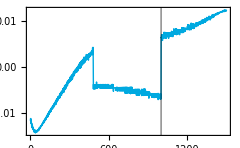

```mathematica
(*Ableitung des Abstands*)
ListLinePlot[
ListConvolve[{1,-1},Table[Norm[hist[[Max@selection]]-r],{r,hist[[Min@selection;;Max@selection+500]]}]],
GridLines->{{Max@selection-Min@selection},None}
]
```

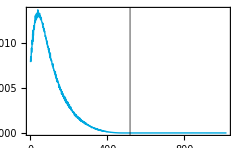

```mathematica
speed=ListConvolve[{{1},{-1}},hist[[Min@selection;;Max@selection+501]]];
ListLinePlot[
Norm/@(((#-speed[[-1]])^2&/@speed)*((#-hist[[Max@selection]])^2&/@hist[[Min@selection;;Max@selection+500]])),
PlotRange->All,
GridLines->{{Max@selection-Min@selection},None}
]
```

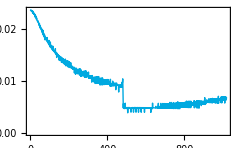

```mathematica
ListLinePlot[Norm/@speed]
```

### aktuell implementierte

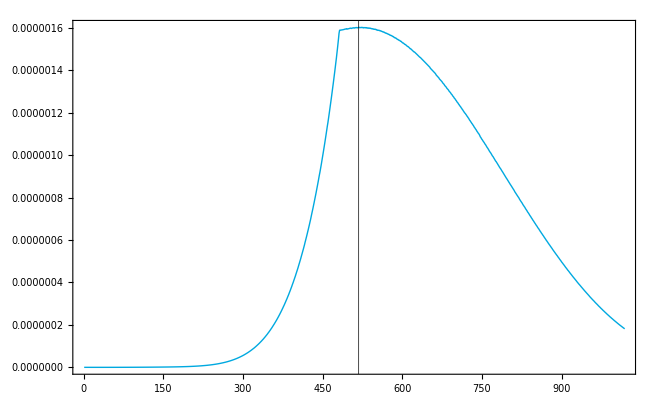

```mathematica
(*implementierte Fehlerfunktion*)
Needs["CCompilerDriver`"];

lib=CreateLibrary[{"mathematicaInterface.c"},"mathematicaErrorFunction"];
errorFunktion=LibraryFunctionLoad[lib,"mathematicaErrorFunction",{Real,Real,Real,Real,Real,Real},Real];

speed=ListConvolve[{{1},{-1}},hist[[Min@selection;;Max@selection+501]]];

ListLinePlot[
Map[errorFunktion[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[6]]]&,Transpose@Flatten[Transpose@{speed,hist[[Min@selection;;Max@selection+500]]},{2,3}]],
GridLines->{{Max@selection-Min@selection},None}
]
```

## Plot trajectory

```mathematica
tra = Import["data/trajectory.dat","Table"];

(*selection = Range[Min@selection,Min@selection + Length@tra-1];*)

(*find closest point between spacecraft and jupiter*)
closestDay=Ordering[Norm/@(jupiter[[2;;Length@tra+1]]-tra),{1}][[1]];

errpoints = {{-4.679722,1.663046,-1.381067},{-2.612807,0.575171,-2.708756},{-4.300980,2.048850,1.566730}};

plt=Graphics3D[{
(*Planet Orbits*)
Black,AbsolutePointSize[6],
Line@jupiter[[ 2;;Length@tra]],
Line@earth[[ 2;;Length@tra]],
Point[{0,0,0}],
AbsolutePointSize[4],
Point@jupiter[[closestDay+1;;closestDay+1+3]],

(*historic Trajectory*)
RGBColor[0.880722, 0.611041, 0.142051],
Line@hist[[1;;Min@selection + Length@tra]],
AbsolutePointSize[6],
Point@hist[[enddays+Min@selection]],

(*simulation*)
RGBColor[0., 0.6627450980392157, 0.8784313725490196],
Line[tra],
Point@tra[[closestDay;;closestDay+3]],
AbsolutePointSize[6],
Point@tra[[enddays]]

},
Boxed->False,
Axes->True,
AxesLabel->{"x in AU","y in AU","z in AU"},
AxesStyle->Directive[10,FontColor->Black,FontFamily->"Times"],
ImageSize->Large,

FaceGrids->{{1,0,0},{0,0,-1},{0,-1,0}},
ViewVertical->{0,0,1},ViewPoint->{-2.2,2.4,0.8},
ViewProjection->"Orthographic",
AspectRatio->Automatic
]
Export["img/trajectorySimulated.pdf",plt];
Export["img/trajectorySimulated.png",plt,ImageResolution->500];

(*plt = Show[plt,PlotRange->{{-5.5,-4.5},{1.5,2.5},{-.5,.5}}]*)
plt = Show[plt,PlotRange->{{-5.2,-4.8},{1.9,2.2},{-.1,.3}}]
Export["img/trajectorySimulatedDetailed.pdf",plt];
Export["img/trajectorySimulatedDetailed.png",plt,ImageResolution->500];

(*Show[plt,ViewPoint->{0, 0,1},Axes->{True,True,False},ViewVertical->{0,-1,0}]
Show[plt,ViewPoint->{0, 1,0},Axes->{True,False,True}]*)
```

-Graphics3D-

-Graphics3D-

## Grid Search

```mathematica
(*grid=Import["data/gridSearch.dat","Table"][[1;;-1]];*)
grid = Flatten[Import[#,"Table"]&/@FileNames["data/gridSearch0*.dat"],1]; 

max = SortBy[grid,Last][[-1,4;;6]];

(*grid = grid[[All,{1,2,3,7}]];*)
grid = grid[[All,{4,5,6,7}]];
grid[[All,4]]=1/grid[[All,4]];

(*select only specific part*)
grid=Select[grid,(-0.009478<#[[1]]<-0.00946)&];
max = SortBy[grid,Last][[-1]];
N[max,15]


(*inter=Interpolation[Transpose@{grid[[All,1;;3]],grid[[All,4]]}];
max = NMaximize[{
inter[x,y,z],
Min@grid[[All,1]]<x<Max@grid[[All,1]],
Min@grid[[All,2]]<y<Max@grid[[All,2]],
Min@grid[[All,3]]<z<Max@grid[[All,3]],
z>0
},{x,y,z}][[2,All,2]]*)

max = SortBy[grid,Last][[-1,1;;3]];

plt =Show[{
ListDensityPlot3D[grid,
ColorFunction->"SunsetColors",
OpacityFunction->(#^1.5&),
AxesLabel->{"v_x","v_y","v_z"},
Boxed->False,Axes->True,
ViewProjection->"Orthographic"
],
Graphics3D[{
Point@max
}]
}]

Export["img/gridSearch.pdf",plt];
Export["img/gridSearch.png",plt,ImageResolution->500];
```

{-0.00946414,0.0217442,0.00081338,1987.75}

-Graphics3D-

```mathematica
(*for performance calculation*)
8*(20*20*20)//N (*grid points*)
%/61
%/60 (*minutes*)
%/60(*hours*)
```

64000.

1049.18

17.4863

0.291439

```mathematica
(*get vector between two local maxima*)
vec = Normalize[{-0.0094182634,0.0217257274,0.0008195859}-{-0.0093982634,0.0217177274,0.0008225859}]
(*get third vector for coordinate system*)
Cross[vec,{0,0,1}]
```

{-0.919601,0.36784,-0.13794}

{0.36784,0.919601,0.}

```mathematica
(*Mathematica for Parallelisation and c for the trajectory*)
Needs["CCompilerDriver`"];

lib=CreateLibrary[{"mathematicaInterface.c"},"mathematicaTrajectoryError"];
trajectoryError=LibraryFunctionLoad[lib,"mathematicaTrajectoryError",{Real,Real,Real},Real];

gridRes = 0.00005;
cGrid = ParallelTable[{x,y,z,trajectoryError[x,y,z]^-1},{x,-0.01,0,gridRes},{y,0.021,0.0215,gridRes},{z,0.0005,0.002,gridRes}];//EchoTiming

ListDensityPlot3D[Flatten[cGrid,{1,2,3}],
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
AxesLabel->{"v_x","v_y","v_z"},
PlotLabel->"Error^-1",
OpacityFunction->(#^2&),
AspectRatio->Full,
ViewProjection->"Orthographic"
]
```

37.7413

-Graphics3D-

## Calculate error

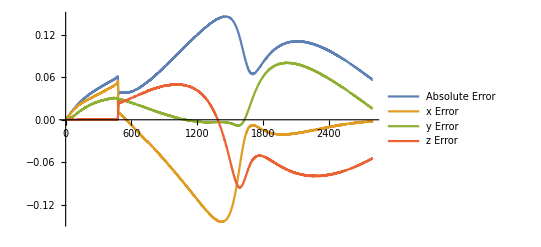

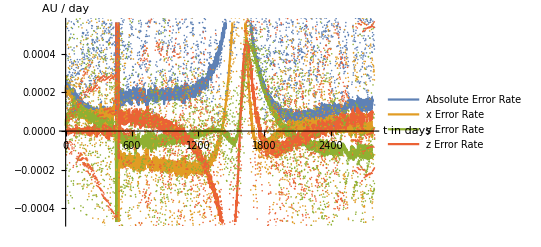

```mathematica
tra = Import["data/trajectory.dat"];
selection = Range[Min@selection,Min@selection + Length@tra-1];

(*Error*)
diff=hist[[Min@selection;;Min@selection + Length@tra-1]]-tra;
ListLinePlot[{
Norm/@diff,
diff[[All,1]],
diff[[All,2]],
diff[[All,3]]
},
PlotLegends->{
"Absolute Error",
"x Error",
"y Error",
"z Error"
},
FrameLabel->{"t in days", "AU"}
]

(*Error Rate*)
diffRate = DerivativeFilter[diff,{1}];

diffRateSmooth = MovingAverage[diffRate,20];
Show[{ListLinePlot[{
Norm/@diffRateSmooth,
diffRateSmooth[[All,1]],
diffRateSmooth[[All,2]],
diffRateSmooth[[All,3]]
},
PlotLegends->{
"Absolute Error Rate",
"x Error Rate",
"y Error Rate",
"z Error Rate"
},
AxesLabel->{"t in days", "AU / day"}
],
ListPlot[{
Norm/@diffRate,
diffRate[[All,1]],
diffRate[[All,2]],
diffRate[[All,3]]
}
]
}]
```

```mathematica
Graphics3D[
{
RGBColor[0.880722, 0.611041, 0.142051],
Line@hist[[selection]],
RGBColor[0., 0.6627450980392157, 0.8784313725490196],
Line@tra,
Red,
Line[tra[[1;;Length@diffRateSmooth]]+1000*diffRateSmooth],
Black,
Point@{0,0,0}
},
Boxed->False
]
```

-Graphics3D-

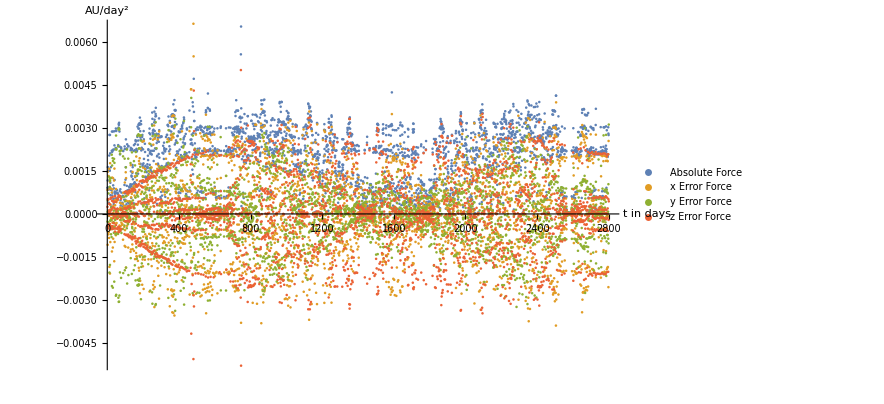

```mathematica
diffForce = DerivativeFilter[diff,{2}];

ListPlot[{
Norm/@diffForce,
diffForce[[All,1]],
diffForce[[All,2]],
diffForce[[All,3]]
},
PlotLegends->{
"Absolute Force",
"x Error Force",
"y Error Force",
"z Error Force"
},
AxesLabel->{"t in days", "AU/day^2"}
]
```

## Numeric

```mathematica
planetMasses=Transpose[#[[1,1]]&/@{jupiter,earth,sun}];
planetPos = ListInterpolation[Transpose@{Range@Length@#[[2;;-1]],#[[2;;-1]]}]&/@{jupiter,earth,sun};
```

```mathematica
g=UnitConvert[Quantity[, "GravitationalConstant"],"AstronomicalUnit"^3/("Kilograms" "Days"^2)]//QuantityMagnitude;
force[t_,r_]:=Sum[g* planetMasses[[i]] (planetPos[[i]][t]-r)/Norm[planetPos[[i]][t]-r]^3,{i,Length@planetPos}]
```

```mathematica
NDSolve[{
force[t,{x[t],y[t],z[t]}]== {x''[t],y''[t] , z''[t]},
{x[1],y[1],z[1]}=={0.9018647801517535,0.4249622724991888,0.007482330796928186},
{x'[1],y'[1],z'[1]}=={-0.0094621291,0.0217432123,0.0008138193}
},{x,y,z},{t,1,2500}]
```

```mathematica
NDSolve[{
force[t,{x[t],y[t],z[t]}][[1]]== x''[t],
force[t,{x[t],y[t],z[t]}][[2]]== y''[t],
force[t,{x[t],y[t],z[t]}][[3]]== z''[t],
x[1]==0.9018647801517535,
y[1]==0.4249622724991888,
z[1]==0.007482330796928186,
x'[1]==-0.0094621291,
y'[1]==0.0217432123,
z'[1]==0.0008138193
},{x,y,z},{t,1,2500}]
```

NDSolve::ndfdmc: Computed derivatives do not have dimensionality consistent with the initial conditions.

NDSolve[{(0.000295916 (-x[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)+(2.82477×10^-7 (-x[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)+(8.88774×10^-10 (-x[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)==x''[t],(0.000295916 (-y[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)+(2.82477×10^-7 (-y[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)+(8.88774×10^-10 (-y[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)==y''[t],(0.000295916 (-z[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)+(2.82477×10^-7 (-z[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)+(8.88774×10^-10 (-z[t]+InterpolatingFunction[…][t]))/(Abs[-x[t]+InterpolatingFunction[…][t]]^2+Abs[-y[t]+InterpolatingFunction[…][t]]^2+Abs[-z[t]+InterpolatingFunction[…][t]]^2)^(3/2)==z''[t],x[1]==0.901865,y[1]==0.424962,z[1]==0.00748233,x'[1]==-0.00946213,y'[1]==0.0217432,z'[1]==0.000813819},{x,y,z},{t,1,2500}]